# Multiway Powersort

Code to reproduce plots from “Multiway Powersort”

## Setup

### Running Times csv tools

```mathematica
Needs["ErrorBarPlots`"]
read[filename_]:=With[{raw=Import[filename]},header=raw⟦1⟧;removeComments[raw⟦2;;⟧]]
removeComments[data_]:=Select[data,¬StringQ[#⟦1⟧]∨Characters[#⟦1⟧]⟦1⟧≠"#"&]
col[field_]:=With[{p=Position[header,field]},If[p=={},Throw["Field "<>field<>" not found in csv header."],p⟦1,1⟧]];
algos[data_]:=algos[data]=Union[data⟦;;,col["algo"]⟧]
realAlgos[data_]:=Complement [algos[data],{"nop","random-shuffle"}]
sizes[data_]:=sizes[data]=Union[data⟦;;,col["n"]⟧]
times[data_,algo_,n_]:=Select[data,#⟦col["algo"]⟧===algo∧#⟦col["n"]⟧===n&]⟦;;,col["ms"]⟧
mergecosts[data_,algo_,n_]:=  Select[data,#⟦col["algo"]⟧===algo∧#⟦col["n"]⟧===n&]⟦;;,col["merge-cost"]⟧
buffercosts[data_,algo_,n_]:=Select[data,#⟦col["algo"]⟧===algo∧#⟦col["n"]⟧===n&]⟦;;,col["buffer-cost"]⟧
comparisons[data_,algo_,n_]:=Select[data,#⟦col["algo"]⟧===algo∧#⟦col["n"]⟧===n&]⟦;;,col["comparisons"]⟧
normMergeCosts[data_,algo_,n_]:=1/(n Log2[n])Select[data,#⟦col["algo"]⟧===algo∧#⟦col["n"]⟧===n&]⟦;;,col["merge-cost"]⟧
meanTimesErrors[data_,algo_]:=Table[With[{ts=times[data,algo,n]},{{Log[10,n],Mean[ts]},ErrorBar[StandardDeviation[ts]]}],{n,sizes[data]}]
normMeanTimesErrors[data_,algo_]:=Table[With[{ts=times[data,algo,n]},{{Log[10,n],Mean[(10^6 ts)/(n Log2[n])]},ErrorBar[StandardDeviation[(10^6 ts)/(n Log2[n])]]}],{n,sizes[data]}]
normMeanMergeCostsErrors[data_,algo_]:=Table[With[{ts=mergecosts[data,algo,n]},{{Log[10,n],Mean[(ts)/(n Log2[n])]},ErrorBar[StandardDeviation[(ts)/(n Log2[n])]]}],{n,sizes[data]}]
normError[data_,algo_,n_]:=With[{ts=times[data,algo,n]},{Mean[(10^6 ts)/(n Log2[n])],StandardDeviation[(10^6 ts)/(n Log2[n])]}]
meansStdevs[data_]:=Table[With[{ts=times[data,algo,n]},With[{μ=Mean[ts],σ=StandardDeviation[ts]},{algo,n,μ,μ-σ,μ+σ}]],{algo,algos[data]},{n,sizes[data]}];

(*from https://reference.wolfram.com/language/howto/AddErrorBarsToChartsAndPlots.html*)
errorBar[type_: "Rectangle"][{{x0_,x1_},{y0_,y1_}},value_,meta_]:=Block[{error,mags=QuantityMagnitude[value]},error=Flatten[QuantityMagnitude[meta]];
error=If[error==={},0,Last[error]];{ChartElementData[type][{{x0,x1},{y0,y1}},mags,meta],{Gray,Dashing[1],Line[{{{(x0+x1)/2,y1-error},{(x0+x1)/2,y1+error}},{{1/4 (3 x0+x1),y1+error},{1/4 (x0+3 x1),y1+error}},{{1/4 (3 x0+x1),y1-error},{1/4 (x0+3 x1),y1-error}}}]}}]

aggregateTimesTable[data_]:=Module[{},
{{"n"}~Join~Table[#<>"-"<>algo&/@{
"mean",
"stdev",
"mean-norm",
"stdev-norm"
},{algo,algos[data]}]//Flatten}
~Join~
Table[{n}~Join~Flatten[Table[With[{ts=times[data,algo,n]},{
N@Mean[ts],
N@StandardDeviation[ts],
N@Mean[(10^6 ts)/(n Log2[n])],
N@StandardDeviation[(10^6 ts)/(n Log2[n])]
}],
{algo,algos[data]}]],{n,sizes[data]}]
];

aggregateMergeCostsTable[data_]:=Module[{},
{{"n"}~Join~Table[#<>"-"<>algo&/@{
"mean",
"stdev",
"mean-norm",
"stdev-norm"
},{algo,algos[data]}]//Flatten}
~Join~
Table[{n}~Join~Flatten[Table[With[{mc=mergecosts[data,algo,n]},{
N@Mean[mc],
N@StandardDeviation[mc],
N@Mean[mc/(n Log2[n/24])],
N@StandardDeviation[mc/(n Log2[n/24])]
}],
{algo,algos[data]}]],{n,sizes[data]}]
];
```

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
FileNames["*times-runs*cmps*csv",NotebookDirectory[]]
```

{}

### Data files

```mathematica
csvPath=NotebookDirectory[];
csvFilesRandomRuns=FileNames["*times-runs*int*csv",csvPath];
csvFilesRandomRunsLongPointer=FileNames["*times-runs*l+p*csv",csvPath];
csvFilesRP=FileNames["*times-rp*int*csv",NotebookDirectory[]];
csvFilesCmp=FileNames["*times-runs*cmps*csv",NotebookDirectory[]];
```

### Sanity checks on running times

```mathematica
checkAllFiles[csvfiles_,algo_]:=Table[
Module[{data,n,reps,ts},
Print[csv];
data=read[csv];
Print[algos[data]];
n=sizes[data][[-1]];
ts=times[data,algo,n];
reps=Length[ts];
Print[Histogram[ts,reps,PlotLabel->csv]];
Print[ListPlot[ts,Joined->True,PlotRange->All]];
]
,{csv,csvfiles}]
```

```mathematica
checkAllFiles[csvFilesRandomRuns,"TopDownMergesort+iscutoff=24+checkSorted=1+mergingMethod=COPY_BOTH"]
```

### Plot configuration

```mathematica
shortenNamesMulti={
"PowerSort4Way+minRunLen=24+mergeMethod=WILLEM_TUNED+onlyIncRuns=0"->"4-way Powersort",
"PowerSort4Way+minRunLen=24+mergeMethod=GENERAL_BY_STAGES_SPLIT+onlyIncRuns=0"->"4-way Powersort\n(no sentinels)",
"PowerSort+minRunLen=24+onlyIncRuns=0+mergingMethod=COPY_BOTH_WITH_SENTINELS"->"2-way Powersort",
"PowerSort+minRunLen=24+onlyIncRuns=0+mergingMethod=COPY_BOTH"->"2-way Powersort\n(no sentinels)",
"PowerSort+minRunLen=24+onlyIncRuns=0+mergingMethod=COPY_SMALLER"->"2-way Powersort\n(buffer smaller run only)",
"std::sort"->"std::sort",
"std::stable_sort"->"std::stable_sort",
"TopDownMergesort+iscutoff=24+checkSorted=1+mergingMethod=COPY_BOTH"->"top-down mergesort"
};
myAlgos=shortenNamesMulti[[;;5,1]];
allAlgos=shortenNamesMulti[[;;,1]];
scannedElAlgos=shortenNamesMulti[[{1,5,3,8},1]];
```

```mathematica
withMergecosts={"systemsort"->Nothing,"Timsort-library"->Nothing};
myDashed=Dashing[{0.02,0.008}];
plotStylesMulti={
"PowerSort+minRunLen=24+onlyIncRuns=0+mergingMethod=COPY_BOTH_WITH_SENTINELS"->Directive[Blue],
"PowerSort+minRunLen=24+onlyIncRuns=0+mergingMethod=COPY_BOTH"->Directive[Blue,myDashed],
"PowerSort+minRunLen=24+onlyIncRuns=0+mergingMethod=COPY_SMALLER"->Directive[Darker[Blue],Dashing[{.01,.01}],Thickness[.01]],
"TopDownMergesort+iscutoff=24+checkSorted=1+mergingMethod=COPY_BOTH"->Directive[Orange],
"PeekSort+iscutoff=2+onlyIncRuns=false"->Directive[Orange,myDashed],
"PowerSort4Way+minRunLen=24+mergeMethod=WILLEM_TUNED+onlyIncRuns=0"->Directive[Darker[Green]],
"PowerSort4Way+minRunLen=24+mergeMethod=GENERAL_BY_STAGES_SPLIT+onlyIncRuns=0"->Directive[Darker[Green],myDashed],
"Timsort-library"->Directive[Black,Thick,Dotted],
"Timsort-JDK8"->Directive[Black,Thick,Dotted],
"TimsortStrippedDown"->Directive[Black,noCutoffModifier],
"TimsortTrot"->Directive[Black],
"systemsort"->Directive[Lighter[Gray],Thick,Dotted],
"std::sort"->Directive[Lighter[Gray],Thick],
"std::stable_sort"->Directive[Lighter[Gray],Thick,myDashed]
};
```

## Plots

```mathematica
runs=Flatten[read/@(csvFilesRandomRuns),1];
runsLP=Flatten[read/@(csvFilesRandomRunsLongPointer),1];
rp=Flatten[read/@(csvFilesRP),1];
cmps=Flatten[read/@(csvFilesCmp),1];
```

### Figure 3 (running time over n, ints, random runs)

```mathematica
meansErrorsRunsAll=Table[normMeanTimesErrors[runs,algo],{algo,allAlgos}];
```

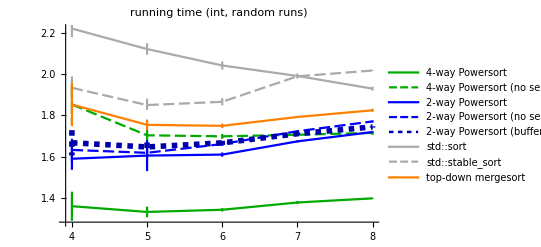

```mathematica
ErrorListPlot[meansErrorsRunsAll,Joined->True,BaseStyle->{FontFamily->"CMU Sans Serif Demi Condensed",FontSize->14},PlotLegends->(Style[#,FontFamily->"CMU Sans Serif Demi Condensed",FontSize->16]&/@(allAlgos/.shortenNamesMulti)),
PlotStyle->(allAlgos/.plotStylesMulti),ImageSize->{400,300},PlotLabel->"running time (int, random runs)"]
Export[NotebookDirectory[]<>"norm-times-ints-runs-sqrtn.pdf",%]
```

### Figure 4 (running time distribution, 10^7 ints, random runs)

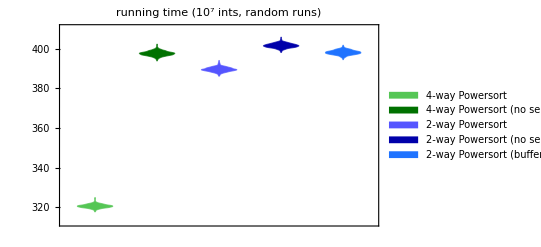

```mathematica
Table[Legended[times[runs,algo,10^7],Style[algo/.shortenNamesMulti,FontFamily->"CMU Sans Serif Demi Condensed",FontSize->16]],{algo,myAlgos}];
DistributionChart[%,BaseStyle->{FontFamily->"CMU Sans Serif Demi Condensed",FontSize->14},ChartStyle->({Directive[Lighter[RGBColor[0, Rational[2, 3], 0]]],Directive[Darker[RGBColor[0, Rational[2, 3], 0]]],Directive[Lighter[RGBColor[0, 0, 1]]],Directive[Darker[RGBColor[0, 0, 1]]],Directive[RGBColor[0.12, 0.45, 1.]],Directive[RGBColor[0.6666666666666666, 0.6666666666666666, 0.6666666666666666],Thickness[Large],Dashing[{Small,Small}]]}), ChartElementFunction->"SmoothDensity",PlotLabel->"running time (10^7 ints, random runs)"]
Export[NotebookDirectory[]<>"times-dist-10M-int-runs-sqrtn.pdf",%]
```

### Figure 5 (running time over n, records, random runs)

```mathematica
meansErrorsRunsAllLp=Table[normMeanTimesErrors[runsLP,algo],{algo,allAlgos}];
```

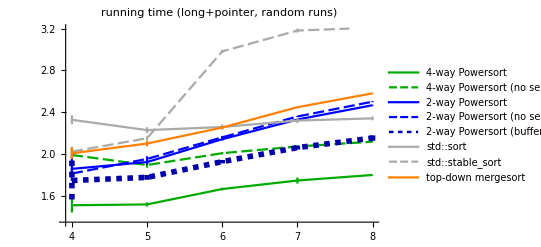

```mathematica
ErrorListPlot[meansErrorsRunsAllLp,Joined->True,BaseStyle->{FontFamily->"CMU Sans Serif Demi Condensed",FontSize->14},PlotLegends->(Style[#,FontFamily->"CMU Sans Serif Demi Condensed",FontSize->16]&/@(allAlgos/.shortenNamesMulti)),
PlotStyle->(allAlgos/.plotStylesMulti),PlotRange->{1.35,3.2},ImageSize->{400,300},PlotLabel->"running time (long+pointer, random runs)"]
Export[NotebookDirectory[]<>"norm-times-l+p-runs-sqrtn.pdf",%]
```

### Figure 6 (running time over n, ints, random permutations)

```mathematica
meansErrorsRp=Table[normMeanTimesErrors[rp,algo],{algo,allAlgos}];
```

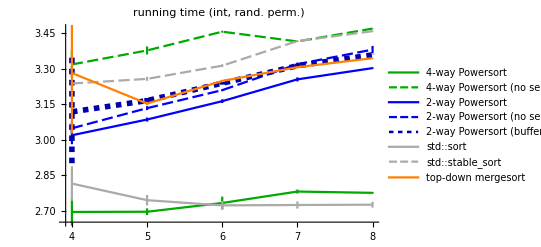

```mathematica
ErrorListPlot[meansErrorsRp,Joined->True,BaseStyle->{FontFamily->"CMU Sans Serif Demi Condensed",FontSize->14},PlotLegends->(Style[#,FontFamily->"CMU Sans Serif Demi Condensed",FontSize->16]&/@(allAlgos/.shortenNamesMulti)),
PlotStyle->(allAlgos/.plotStylesMulti),ImageSize->{400,300},PlotLabel->"running time (int, rand. perm.)"]
Export[NotebookDirectory[]<>"norm-times-ints-rp.pdf",%]
```

### Figure 7 (scanned elements over n, random runs)

```mathematica
meansErrorsScannedElementsRuns=Table[Table[With[{ms=N[mergecosts[cmps,algo,size ]/(size Log2[size/24])],bs=N[buffercosts[cmps,algo,size ]/(size Log2[size/24])]},{{Log[10,size],Mean[2ms+2bs]},ErrorBar[StandardDeviation[2ms+2bs]]}],{size,sizes[cmps]}]
,{algo, scannedElAlgos}
];
```

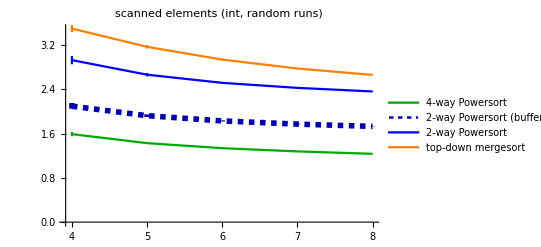

```mathematica
ErrorListPlot[meansErrorsScannedElementsRuns,Joined->True,BaseStyle->{FontFamily->"CMU Sans Serif Demi Condensed",FontSize->14},PlotLegends->(Style[#,FontFamily->"CMU Sans Serif Demi Condensed",FontSize->16]&/@(scannedElAlgos/.shortenNamesMulti)),
PlotStyle->(scannedElAlgos/.plotStylesMulti),ImageSize->{400,300},PlotLabel->"scanned elements (int, random runs)"]
Export[NotebookDirectory[]<>"norm-scanned-elements-ints-runs-sqrtn.pdf",%]
```

### Figure 8 (merge cost over n, random runs)

```mathematica
meansErrorsMergecostRuns=Table[Table[With[{ms=N[mergecosts[cmps,algo,size ]/(size Log2[size/24])]},{{Log[10,size],Mean[ms]},ErrorBar[StandardDeviation[ms]]}],{size,sizes[cmps]}]
,{algo, scannedElAlgos}
];
```

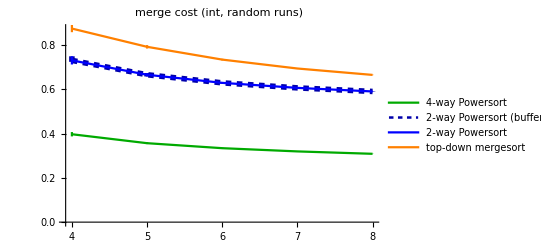

```mathematica
ErrorListPlot[meansErrorsMergecostRuns,Joined->True,BaseStyle->{FontFamily->"CMU Sans Serif Demi Condensed",FontSize->14},PlotLegends->(Style[#,FontFamily->"CMU Sans Serif Demi Condensed",FontSize->16]&/@(scannedElAlgos/.shortenNamesMulti)),
PlotStyle->(scannedElAlgos/.plotStylesMulti),ImageSize->{400,300},PlotLabel->"merge cost (int, random runs)"]
Export[NotebookDirectory[]<>"norm-mergecost-ints-runs-sqrtn.pdf",%]
```